# AMS-511 Foundations of Quantitative Finance

## Fall 2020— Lecture 08 — Wednesday October 27, 2020

## Additional Topics in Options

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Monte Carlo Integration

For certain options the method of choice for pricing them is Monte Carlo simulation. We’ll begin with a review.

Under the risk-neutral measure Q the price dynamics replaces the actual mean with the risk-free mean and keeps the same volatility.

Consider the original example: a call option at time t = 0 with a strike price K = 100 and expiry T = 0.25 years. The risk free rate is r = 6.5%. The underlying asset is currently at the money at S(0) = 100 and has an annual volatility of σ = 30%. Recall that the current price of the option using the Black-Scholes formula is C_0 = 6.77098.

Under the risk-neutral measure the price dynamics are

S(t)=S(0) e^((r - σ^2/2)t + σ W(t))

where W(t)~N[0, √t].

To price a call option we can generate n random samples. Designate the kth such experiment S^(k)(T)=S(0)ⅇ^((r-σ^2/2)T+σ randN[0, √T]), where randN[0, √T] is a function that generates a random number with an N[0, √T] distribution. The Monte Carlo estimate for the integral is

C(S(0),0)=e^(-r T)E^Q[C(S(T),T)]≃e^(-r T)/n(∑_(k=1)^n max[S^(k)(T)-K, 0])

In this instance, we have an  analytical solution for S(T) for comparison. If this were not the case, then we could have proceeded directly from the SDE describing the asset dynamics under the risk neutral measure to simulate the trajectories S^(k)(T).

The approach of replacing the actual drift with the risk-free rate but preserving the original volatility structure is valid under a fairly large number of circumstances. For example, if the risk-free rate or volatility are themselves stochastic processes with their own SDEs, then such situations can be handled without undue complication.

As noted above, if there are proportional dividends δ and storage costs η per unit time, then the appropriate discounting uses the risk-neutral rate r-δ+η.

One problem of Monte Carlo techniques is the standard error of the estimate tends to be proportional to 1/√n, for a sample size of n. However, we have explored only the most simple sampling approach. There are a number of techniques available to increase the efficiency of Monte Carlo integration.

### European Call Option Pricing

Applying standard statistical methodology we can compute the standard deviation of the estimate by dividing the standard deviation of the sample by square root of the sample size. A simulation with  n = 1000 is demonstrated.

#### Code

The function below returns the estimated mean of the call price and the sampling error of the mean.

```mathematica
xEuroCallOptMonteCarlo[nNowPrice_,nVolatility_,nStrikePrice_,nExpiry_,nRiskFree_,iSamples_]:={Mean[#],StandardDeviation[#]/√iSamples}&[Exp[-nRiskFree nExpiry](Max[#-nStrikePrice,0]&/@(nNowPrice Exp[(nRiskFree-nVolatility^2/2.)nExpiry]Exp[ nVolatility RandomVariate[NormalDistribution[0,√nExpiry],iSamples]]))];
```

For example, an at-the-money put is estimated at

```mathematica
xEuroCallOptMonteCarlo[100.,0.3,100.,0.25,0.065,1000]
```

{6.44628,0.312487}

For comparison, the Black-Scholes solution is 6.77098.

### Example II — Plotting the Alternatives

We repeated this process for prices of 85 to 105. The results with ± 1.96 standard errors are plotted against the Black-Scholes results below.

#### Simulation of Estimates with their 95% Confidence Levels

```mathematica
mnSim=Transpose@Block[
{sol},
Table[
sol=xEuroCallOptMonteCarlo[price,0.3,100.,0.25,0.065,10000];
{{price,sol⟦1⟧-1.96sol⟦2⟧},{price,sol⟦1⟧},{price,sol⟦1⟧+1.96sol⟦2⟧}},
{price,85.,105.,5.}
]
]
```

{{{85.,1.15593},{90.,2.26777},{95.,4.13464},{100.,6.60546},{105.,9.59719}},{{85.,1.23814},{90.,2.38177},{95.,4.29341},{100.,6.8056},{105.,9.8369}},{{85.,1.32035},{90.,2.49576},{95.,4.45219},{100.,7.00573},{105.,10.0766}}}

#### Plot Comparing Black-Scholes and the Monte Carlo Solutions

This example uses Mathematica’s FinancialDerivative[] function which uses Black-Scholes for pricing vanilla European options and will be described later in the class. A plot comparing the analytical Black-Scholes prices with the simulated prices and their 95% confidence intervals is

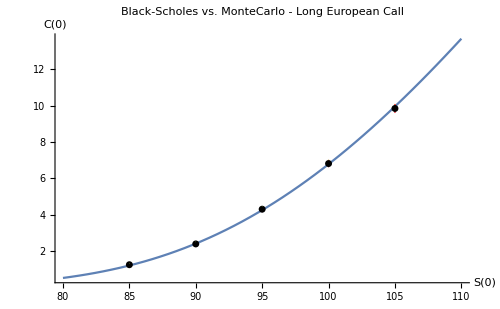

```mathematica
Show[
Plot[FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 100.00, "Expiration"->0.25},  {"InterestRate"-> 0.065, "Volatility" -> 0.3, "CurrentPrice"-> price}],{price,80,110},PlotLabel->Style["Black-Scholes vs. MonteCarlo - Long European Call",FontSize->16],AxesLabel->(Style[#,FontSize->14]&/@{"S(0)","C(0)"})],
ListPlot[mnSim,PlotStyle->{{PointSize[0]},{Black,PointSize[0.01]},{PointSize[0]}},Filling->{1->{3}},FillingStyle->Red],PlotRange->All,ImageSize->500
]
```

## Asian Options

Asian options are among the class of so-called exotic options. The price at expiry is not the final price but some average of the price realized over the life of the option.

### Overview

An Asian option is one whose value is based on the average price observed rather than the price at expiry. Read the Wikipedia article https://en.wikipedia.org/wiki/Asian_option which describes these options in detail.

Consider an Asian arithmetic European put option, its value at expiry at beginning at time 0 with strike price K and expiry T is

P(T)=max[M[0,T]-K,0]

where M[0,T] is the arithmetic average price over the interval 0≤t≤T defined as

M[0,T]=1/T∫_0^T S(t)ⅆt

Note that M[0,T] is a random variable.

Alternately, the option may define the arithmetic average as computed by averaging the price at fixed intervals,

M[0,T]=1/N∑_(i=0)^(N-1) S(t_i)

but here we will only consider the first (integral) definition of M[0,T] above.

Other forms of the Asian option use a different method of computing M[0,T]. For example, the geometric average is sometimes used:

M[0,T]=Exp[∫_0^T Log[S(t)]ⅆt]

Some forms of Asian options have an analytical solution, but the arithmetic case does not. A common means of estimation is Monte Carlo.

### FinancialDerivative[ ]

Mathematica’s FinancialDerivative[ ] function can be used to estimate the value of an Asian arithmetic European put. Here we have S(0)=95.00, K=100.00, T=1, r_f=0.02, and σ=0.10.

```mathematica
FinancialDerivative[{"AsianArithmetic","European","Put"},{"StrikePrice"->100.,"Expiration"->1.,"Inception"->0.,"AverageSoFar"->95.},
{"CurrentPrice"->95.,"Volatility"->0.10,"InterestRate"->0.02}]
```

4.67986

### Monte Carlo

In a Monte Carlo framework the integral above for the average price can be approximated by a discrete sum. Note in the vanilla European case we were able to exploit the solution to the constant coefficient Itô process under the risk-neutral measure Q:

S(t)=S(0) ⅇ^((r - σ^2/2)t + σ W(t))

where W(t)\[Distributed]N[0,√t].

We can also use this solution to generate a path of prices in time increments of Δ by

S(t+Δ)=S(t) ⅇ^((r - σ^2/2)Δ + σ W(Δ))

where W(Δ)\[Distributed]N[0,√Δ].

Using Mathematica’s notation, the above is

S(t+Δ)=S(t) Exp[(r - σ^2/2)Δ + σ RandomVariate[NormalDistribution[0.,√Δ]]

Once we have generated a single sample path we label j then we can compute its mean

M^(j)[0,T]=1/(T/Δ+1)∑_(k=0)^(T/Δ) S^(j)(i Δ)

and the option price

P^(j)(T)=max[K-M^(j)[0,T],0]

If we repeat this experiment J times, then to estimate the option price

P̂[0]=Exp[-r T]/J∑_(j=1)^J P^(j)[T]≃ⅇ^(-r T)𝔼_Q[P[T]]

Note that we need to compute two Monte Carlo simulations: An inner one to estimate the mean price for each sample price path, and an outer one to estimate the discounted risk neutral expectation of a number sampled option valuations.

### Approach

Let δ denote some result which returns the random result below each time it is called:

δ≡(r - σ^2/2)Δ + σ RandomVariate[NormalDistribution[0.,√Δ]]

The the price dynamics can be characterized by

S(0)=S(0) Exp[0]

S(Δ)=S(0) Exp[0+δ_1]

S(2Δ)=S(0) Exp[0+δ_1+δ_2]

⋮

S(k Δ)=S(0) Exp[0+δ_1+δ_2+…+δ_k]

We can succinctly generate a sample path of S(t) using FoldList[ ] to recursively compute

{S(0),S(Δ), …,S(k×Δ)}=S(0) Exp[FoldList[Plus,0,{δ_1+δ_2+…+δ_k}]]

where we set k so that T=k×Δ. Note that we can generate a k-vector δ⃗ using

δ⃗=(r - σ^2/2)Δ + σ RandomVariate[NormalDistribution[0.,√Δ],k]

The average price for a sample path is, therefore,

M[0,T]=Mean[S(0) Exp[FoldList[Plus,0,δ⃗]]]

If we repeat this experiment J times, then to estimate the option price

P̂[0]=Exp[-r T]/J∑_(j=1)^J P^(j)[T]≃ⅇ^(-r T)𝔼_Q[P[T]]

#### Code

We only need a single line of code to compute the Monte Carlo estimate, including the simulation’s standard error. Whether you express your function as a single line or break it up into multiple lines depends upon both clarity and efficiency. For an experienced programmer figuring out the logic of the code below would not be difficult, but there is no problem breaking it into separate steps if you find that clearer or more maintainable. Here’s a rather coarse path using Δ=0.1 as an illustration. Note that I=T/Δ=1/0.1.

```mathematica
95. Exp[FoldList[Plus,0.,(0.02-0.10^2/2.)0.1+0.10 RandomVariate[NormalDistribution[0.,√0.1],1./0.1]]]
```

{95.,94.9484,97.2008,99.2296,106.08,107.749,106.205,103.628,105.965,104.699,101.589}

In terms of the variables described above we define a function

xAsianArithPutMonteCarlo[S(0),σ,K,T,Δ,r,I,K]

```mathematica
xAsianArithPutMonteCarlo[nInitialPrice_,nVolatility_,nStrikePrice_,nExpiry_,nDeltaT_,nRiskFree_,iDeltaSteps_,iNSamples_]:=
{Mean[#],StandardDeviation[#]/√iNSamples}&[Exp[-nRiskFree nExpiry]Table[
Max[nStrikePrice-Mean[nInitialPrice Exp[FoldList[Plus,0.,(nRiskFree-nVolatility^2/2.)nDeltaT+nVolatility RandomVariate[NormalDistribution[0.,√nDeltaT],iDeltaSteps]]]],0],{iNSamples}]]
```

```mathematica
xAsianArithPutMonteCarlo[95.,0.1,100.,1.,0.0005,0.02,1./0.0005,1000.]
```

{4.69019,0.133866}

```mathematica
xAsianArithPutMonteCarlo[95.,0.1,100.,1.,0.0001,0.02,1./0.0001,1000.]
```

{4.73251,0.132981}

The simulation study below returns a vector of points representing the underlying price at various levels vs. the lower 95% confidence limit, mean, and upper 95% confidence limit for the option price. The vector of such results is then transposed to yield three lines representing the lower confidence level, mean, and upper confidence level.

```mathematica
mnSim=Transpose@Block[
{sol},
Table[
sol=xAsianArithPutMonteCarlo[price,0.1,100.,1.,0.0005,0.02,1./0.0005,1000.];
{{price,sol⟦1⟧-1.96sol⟦2⟧},{price,sol⟦1⟧},{price,sol⟦1⟧+1.96sol⟦2⟧}},
{price,80.,120.,5.}
]
]
```

{{{80.,18.5785},{85.,13.6277},{90.,8.79182},{95.,4.53568},{100.,1.5766},{105.,0.384248},{110.,0.0361857},{115.,-0.00092504},{120.,-0.000998841}},{{80.,18.8577},{85.,13.9406},{90.,9.10691},{95.,4.79543},{100.,1.75179},{105.,0.47424},{110.,0.0656307},{115.,0.00716093},{120.,0.00208103}},{{80.,19.1369},{85.,14.2535},{90.,9.42199},{95.,5.05518},{100.,1.92697},{105.,0.564232},{110.,0.0950756},{115.,0.0152469},{120.,0.00516091}}}

A comparison of our solutions and those of Mathematica’s FinancialDerivative[ ] follows.

```mathematica
mnSim[[2]]
```

{{80.,18.8577},{85.,13.9406},{90.,9.10691},{95.,4.79543},{100.,1.75179},{105.,0.47424},{110.,0.0656307},{115.,0.00716093},{120.,0.00208103}}

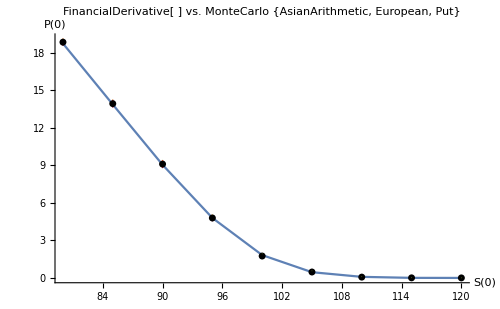

```mathematica
Show[
ListLinePlot[Table[{price,FinancialDerivative[{"AsianArithmetic","European","Put"},{"StrikePrice"->100.,"Expiration"->1.,"Inception"->0.,"AverageSoFar"->95.},
{"CurrentPrice"->price,"Volatility"->0.10,"InterestRate"->0.02}]},{price,80,120,5}],PlotLabel->Style["FinancialDerivative[ ] vs. MonteCarlo\n{AsianArithmetic, European, Put}",FontSize->16],AxesLabel->(Style[#,FontSize->14]&/@{"S(0)","P(0)"})],
ListPlot[mnSim,PlotStyle->{{PointSize[0]},{Black,PointSize[0.01]},{PointSize[0]}},Filling->{1->{3}},FillingStyle->Red],PlotRange->All,ImageSize->500
]
```

Again, note that the Mathematica function itself uses Monte Carlo. It returns a slightly different result each time it is run. We’ll sample it to see how much it varies from call to call.

```mathematica
vnMmaSim=Table[FinancialDerivative[{"AsianArithmetic","European","Put"},{"StrikePrice"->100.,"Expiration"->1.,"Inception"->0.,"AverageSoFar"->95.},
{"CurrentPrice"->95.,"Volatility"->0.10,"InterestRate"->0.02}],{100}];
```

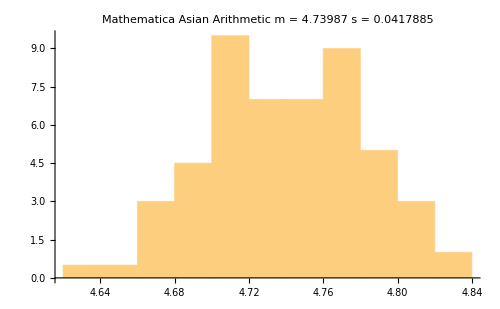

```mathematica
Histogram[vnMmaSim,Automatic,"PDF",PlotLabel->Style["Mathematica Asian Arithmetic\n m = "<>ToString[Mean[vnMmaSim]]<>" s = "<>ToString[StandardDeviation[vnMmaSim]],FontSize->16],ImageSize->500]
```

## American Options

American options are distinguished from European by the fact that the holder of the option has the right to exercise at any time during the life of the contract, not just at expiry. Unlike European options there is no closed form solution to the pricing of American options.

The differences in value between American and European options is explored in https://en.wikipedia.org/wiki/Option_style#Difference_in_value

Clearly, an American option must be worth at least as much as a European option with the same provisions, i.e., on the same asset with the same strike price, start date and expiration date.

### American Calls

Assume that the option is active over time 0 ≤ t ≤ T and that the price at time t is S(t) and the strike price is K. If  S(t) ≤  K, then it does not make economic sense to exercise the option.

Hence, assume that  S(t) >  K. If the option is exercised, then payoff received is S(t) –  K. Consider, however, the alternative strategy: You short the stock at time t and then at time T you cover the short by either buying at S(T) or exercising the option. Thus, the price to cover the short is min[S(T),  K]. The net proceeds are

ⅇ^(r(T-t))S(t)-min[S(T), K] >  ⅇ^(r(T-t))(S(t)-K)

Thus, it never makes sense to exercise the call before T and therefore an American call has the same value as a European call.

### American Puts

For an American put, note that the following must hold

P(S(t), t)≥max[K-S(t), 0]

Otherwise, it would be possible to purchase the option and make an immediate profit by exercising it.

Returning to the replicating portfolio, for a European option without early exercise, we concluded that the replicating portfolio Π satisfied

r Π(t)ⅆt=ⅆΠ(t)

Expanding this expression

r (F(t)-(∂F)/(∂S)S(t))ⅆt=((∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2))ⅆt

and rearranging terms gives the Black-Scholes PDE

0=(∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2)+r S(t)(∂F)/(∂S)-r F(t)

With an American option if

r Π(t)ⅆt>ⅆΠ(t)

then the investor would sell the option and deposit the cash but is exposed to the possibility of early exercise. The no-arbitrage argument still applies.

If

r Π(t)ⅆt<ⅆΠ(t)

then the investor would buy the option and borrow cash, but because the option holder has control over the exercise this possibility is not excluded. The no arbitrage argument no longer applies.

Thus, the best no-arbitrage argument we can muster is

r Π(t)ⅆt≥ⅆΠ(t)

or

0≥ⅆΠ(t)-r Π(t)ⅆt

which expands to

0≥(∂P)/(∂t)+1/2 σ^2(S(t))^2(∂^2 P)/(∂S^2)+r S(t)(∂P)/(∂S)-r P(t)

At each point, it either makes sense to exercise the option or continue to hold the option, and

(P(S(t), t)-max[K-S(t), 0]=0)∨((∂P)/(∂t)+1/2 σ^2(S(t))^2(∂^2 P)/(∂S^2)+r S(t)(∂P)/(∂S)-r P(t)=0)

At expiry we can assert

P(S(T), T)≥max[K-S(T), 0]

and we also observe the following limits

lim_(S→0) P(S(t),t)=K, 0≤t≤T

lim_(S→∞) P(S(t),t)=0, 0≤t≤T

### Risk Neutral Pricing

Under the risk neutral measure ℚ (for a non-dividend paying asset this mean μ → r), we have

P(S(0), 0)=max_(0≤t≤T) E^ℚ[ⅇ^(-r t)max[K-S(t)]]

We must seek the maximum over 0≤t≤T and not just at T.

## Pricing American Options

One of the more common techniques for pricing an American option is to apply dynamic programming to a binomial geometric lattice.

https://en.wikipedia.org/wiki/Dynamic_programming

### Overview

Each step of the geometric binomial lattice has the following price dynamics under the risk neutral measure.

S(t) = ⅇ^(-r Δ)(q/(1-q))^T((u S(t))/(S(t) / u))

For a put option, the same risk neutral measure can be applied at each step to value the option. This is done recursively working backwards in time by starting with the leaves of the lattice where we know the value of the option.

P(t) = ⅇ^(-r Δ)(q/(1-q))^T((P_u(t+Δ))/(P_d(t+Δ)))

With an American put we have the issue of early exercise by the holder of the put. A rational investor would seek to maximize his or her economic benefit, but there is a subtle problem: If the holder wishes to make reasonable a decision today to exercise the put, then that holder has to not only consider the immediate benefit from the exercise but the fact that he or she is giving up any expected economic benefit that may have accrued from exercising at a future date.

Consider a single binomial step at t and assume that the prices P_u(t+Δ) and P_d(t+Δ) already include the economic benefit from a potential future exercise. Then the appropriate value for P(t) is

P(t) =max[max[K-S(t),0], ⅇ^(-r Δ)(q/(1-q))^T((P_u(t+Δ))/(P_d(t+Δ)))]

In other words, if the current value of exercising the put right now is greater than the discounted future expected value under the risk neutral measure of holding the option, then the holder exercises; otherwise, the holder simply maintains his or her position. Thus, this recursion tells the owner of the option when to “fold” or to “hold".

The recursion above is an example of dynamic programming.

### Examples

Consider a put with σ = 0.25, K = 55, T = 0.5, r = 0.04.

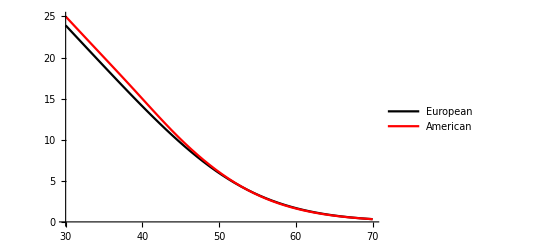

```mathematica
Plot[{
FinancialDerivative[{"European","Put"},{"StrikePrice"->55.00,"Expiration"->0.5},{"InterestRate"->0.04,"Volatility"->0.25,"CurrentPrice"->p}],
FinancialDerivative[{"American","Put"},{"StrikePrice"->55.00,"Expiration"->0.5},{"InterestRate"->0.04,"Volatility"->0.25,"CurrentPrice"->p}]
},
{p,30,70},
PlotStyle->{{Black},{Red}},
PlotLegends->{"European","American"}
]
```

Next consider a put with T = 3.

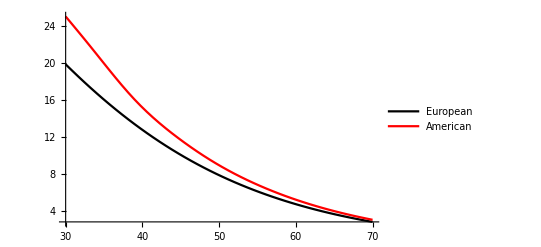

```mathematica
Plot[{
FinancialDerivative[{"European","Put"},{"StrikePrice"->55.00,"Expiration"->3.},{"InterestRate"->0.04,"Volatility"->0.25,"CurrentPrice"->p}],
FinancialDerivative[{"American","Put"},{"StrikePrice"->55.00,"Expiration"->3.},{"InterestRate"->0.04,"Volatility"->0.25,"CurrentPrice"->p}]
},
{p,30,70},
PlotStyle->{{Black},{Red}},
PlotLegends->{"European","American"}
]
```